```mathematica
(*"NSolveOptions"/. SystemOptions[]*)
```

## Planck Black-Body Radiation

```mathematica
f[x_]:=x^3/(Exp[x]-1);
```

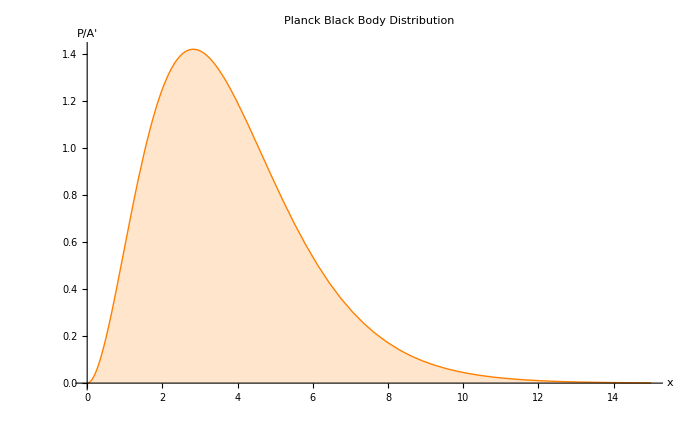

```mathematica
fPlot=Plot[f[x], {x, 0, 15}, AxesLabel->{"x", "P/A'"},Filling->Axis, PlotLabel->"Planck Black Body Distribution", PlotStyle->{Thick, Orange}]
```

```mathematica
df=D[f[x],x]
```

(3 x^2)/(-1+ⅇ^x)-(ⅇ^x x^3)/((-1+ⅇ^x)^2)

```mathematica
TeXForm[df]
```

\frac{3 x^2}{e^x-1}-\frac{e^x x^3}{\left(e^x-1\right)^2}

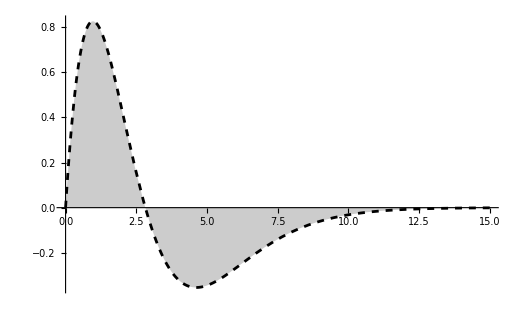

```mathematica
Plot[df, {x,0,15}, PlotRange->All, Filling->Axis, PlotStyle->{Dashed, Black}]
```

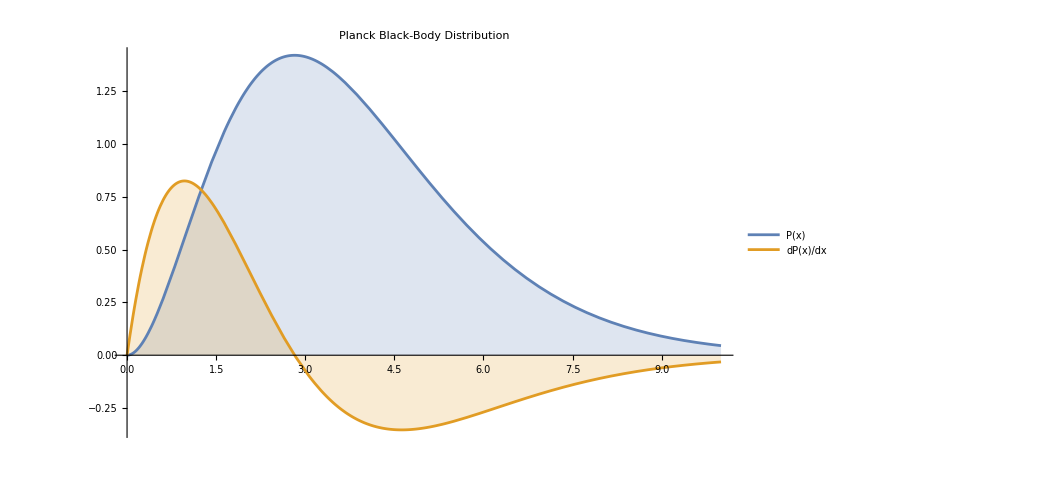

```mathematica
Plot[{f[x],df}, {x, 0, 10}, Filling->Axis, PlotLegends->Placed[{"P(x)", "dP(x)/dx"},{Right,Bottom}], PlotLabel->"Planck Black-Body Distribution"]
```

```mathematica
rf=FindRoot[df==0,{x,2}, Method->"Newton"]
```

{x→2.82144}

```mathematica
params={h->6.62607015*^-34, kB->1.380649*^-23, T->5800, c->2.988*^8}
```

{h→6.62607×10^-34,kB→1.38065×10^-23,T→5800,c→2.988×10^8}

```mathematica
(*Equartion 23.54 Blundell*)
```

```mathematica
λ=(h c)/(2.82144*kB T)
```

(0.354429 c h)/(kB T)

```mathematica
(λ/.params)
```

8.76303×10^-7

```mathematica
(λ/.params)/(1*^-9)
```

876.303

```mathematica
((2.9*^-3)/5800)/(1*^-9)
```

500.

```mathematica
2.8*2
```

5.6

```mathematica
Manipulate[Plot[x^3/(Exp[x/T]-1),{x, 0, 50}, PlotRange->Full], {T, 1,10}]
```

```mathematica
(*Export["plot.mp4",Manipulate[Plot[x^3/(Exp[x/T]-1),{x, 0, 50}, PlotRange->Full, PlotLegends->"Expressions"], {T, 1,10}]]*)
```

```mathematica
(*Wien's Law*)
```

```mathematica
((2.898*^-3)/5800)
```

4.99655×10^-7

```mathematica
((2.898*^-3)/5800)/(1*^-9)
```

499.655

```mathematica
params1={kB->1.380649*^-16, T0->300, NA->6.023*^23, g->980, m->100}
```

{kB→1.38065×10^-16,T0→300,NA→6.023×10^23,g→980,m→100}

```mathematica
T=300;M=18/NA/.params1;
```

```mathematica
h=1/(M g) *((kB T)/m)Log[1/0.9]/.params1
```

1490.04

```mathematica
TeXForm[(4*^12)(3.6*^6)]
```

1.44\times 10^{19}